```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/hybrid_metric-Palatini/math"];
```

## metric-Higgs conformal

```mathematica
hcoord={h1,h2,h3,h4};
coord={h1,h2,h3,h4,Phi};
n=Length[coord];
```

```mathematica
metric=-DiagonalMatrix[{0,0,0,0,1-(6ξ+1)(hcoord.hcoord)/Phi^2}]+DiagonalMatrix[{1,1,1,1,0}]-(6ξ+1)Table[If[i==5&&j!=5,coord[[j]]/Phi,If[i!=5&&j==5,coord[[i]]/Phi,0]],{i,n},{j,n}];
```

```mathematica
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | ((1+6 ξ) (h1+6 h1 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 2, 2] | ((1+6 ξ) (h1+6 h1 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 3, 3] | ((1+6 ξ) (h1+6 h1 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 4, 4] | ((1+6 ξ) (h1+6 h1 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[1, 5, 1] | -(h1 (1+6 ξ) (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[1, 5, 2] | -(h2 (1+6 ξ) (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[1, 5, 3] | -(h3 (1+6 ξ) (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[1, 5, 4] | -(h4 (1+6 ξ) (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[1, 5, 5] | ((h1^2+h2^2+h3^2+h4^2) (1+6 ξ) (h1+6 h1 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 1, 1] | ((1+6 ξ) (h2+6 h2 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 2, 2] | ((1+6 ξ) (h2+6 h2 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 3, 3] | ((1+6 ξ) (h2+6 h2 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 4, 4] | ((1+6 ξ) (h2+6 h2 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[2, 5, 1] | -(h1 (1+6 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 5, 2] | -(h2 (1+6 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 5, 3] | -(h3 (1+6 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 5, 4] | -(h4 (1+6 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[2, 5, 5] | ((h1^2+h2^2+h3^2+h4^2) (1+6 ξ) (h2+6 h2 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 1, 1] | ((1+6 ξ) (h3+6 h3 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 2, 2] | ((1+6 ξ) (h3+6 h3 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 3, 3] | ((1+6 ξ) (h3+6 h3 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 4, 4] | ((1+6 ξ) (h3+6 h3 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[3, 5, 1] | -(h1 (1+6 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 5, 2] | -(h2 (1+6 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 5, 3] | -(h3 (1+6 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 5, 4] | -(h4 (1+6 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[3, 5, 5] | ((h1^2+h2^2+h3^2+h4^2) (1+6 ξ) (h3+6 h3 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[4, 1, 1] | ((1+6 ξ) (h4+6 h4 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 2, 2] | ((1+6 ξ) (h4+6 h4 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 3, 3] | ((1+6 ξ) (h4+6 h4 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 4, 4] | ((1+6 ξ) (h4+6 h4 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[4, 5, 1] | -(h1 (1+6 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[4, 5, 2] | -(h2 (1+6 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[4, 5, 3] | -(h3 (1+6 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[4, 5, 4] | -(h4 (1+6 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[4, 5, 5] | ((h1^2+h2^2+h3^2+h4^2) (1+6 ξ) (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
Γ[5, 1, 1] | (Phi (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 2, 2] | (Phi (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 3, 3] | (Phi (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 4, 4] | (Phi (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 5, 1] | -(h1 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 5, 2] | -(h2 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 5, 3] | -(h3 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 5, 4] | -(h4 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
Γ[5, 5, 5] | ((h1^2+h2^2+h3^2+h4^2) (1+6 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))

```mathematica
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | -(2 Phi^2 (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h1^2 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1^2 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 ξ (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h2+6 h2 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3 ξ (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h3+6 h3 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h4 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h4+6 h4 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(2 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(3 (1+6 ξ)^2)/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
R[2, 1] | -(h1 h2 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 h2 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h1 ξ (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h1+6 h1 ξ) (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[2, 2] | -(2 Phi^2 (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2^2 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2^2 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 ξ (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h1+6 h1 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3 ξ (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h3+6 h3 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h4 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h4+6 h4 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(2 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(3 (1+6 ξ)^2)/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
R[3, 1] | -(h1 h3 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 h3 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h1 ξ (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h1+6 h1 ξ) (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 2] | -(h2 h3 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 h3 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h2 ξ (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h2+6 h2 ξ) (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[3, 3] | -(2 Phi^2 (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3^2 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3^2 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 ξ (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h1+6 h1 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 ξ (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h2+6 h2 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h4 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h4+6 h4 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(2 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(3 (1+6 ξ)^2)/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
R[4, 1] | -(h1 h4 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 h4 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h1 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h1+6 h1 ξ) (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 2] | -(h2 h4 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 h4 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h2 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h2+6 h2 ξ) (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 3] | -(h3 h4 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3 h4 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h3 ξ (1+6 ξ)^2 (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((1+6 ξ)^2 (h3+6 h3 ξ) (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)
R[4, 4] | -(2 Phi^2 (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4^2 (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h4^2 ξ (1+6 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 ξ (1+6 ξ)^2 (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h1+6 h1 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 ξ (1+6 ξ)^2 (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h2+6 h2 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3 ξ (1+6 ξ)^2 (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((1+6 ξ)^2 (h3+6 h3 ξ)^2)/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(2 (1+6 ξ))/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))+(3 (1+6 ξ)^2)/(Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))
R[5, 1] | (2 h1 Phi (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h1 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1^2 (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h2 (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h1+6 h1 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h1 (1+6 ξ)^2 (h2+6 h2 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h3 (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h1+6 h1 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h1 (1+6 ξ)^2 (h3+6 h3 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h1+6 h1 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h1 (1+6 ξ)^2 (h4+6 h4 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 (1+6 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(3 h1 (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
R[5, 2] | (2 h2 Phi (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h2 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h2 (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2 (1+6 ξ)^2 (h1+6 h1 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2^2 (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h1+6 h1 ξ) (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 h3 (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h2+6 h2 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2 (1+6 ξ)^2 (h3+6 h3 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h2+6 h2 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2 (1+6 ξ)^2 (h4+6 h4 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 (1+6 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(3 h2 (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
R[5, 3] | (2 h3 Phi (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h3 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h3 (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3 (1+6 ξ)^2 (h1+6 h1 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 h3 (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3 (1+6 ξ)^2 (h2+6 h2 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3^2 (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h1+6 h1 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h2+6 h2 ξ) (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 h4 (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4 (1+6 ξ)^2 (h3+6 h3 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3 (1+6 ξ)^2 (h4+6 h4 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 (1+6 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(3 h3 (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
R[5, 4] | (2 h4 Phi (1+6 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(12 h4 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 h4 (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4 (1+6 ξ)^2 (h1+6 h1 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 h4 (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4 (1+6 ξ)^2 (h2+6 h2 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 h4 (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4 (1+6 ξ)^2 (h3+6 h3 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h4^2 (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h1 (1+6 ξ)^2 (h1+6 h1 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h2 (1+6 ξ)^2 (h2+6 h2 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(h3 (1+6 ξ)^2 (h3+6 h3 ξ) (h4+6 h4 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h4 (1+6 ξ))/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))-(3 h4 (1+6 ξ)^2)/(Phi (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))
R[5, 5] | -(2 h1 (1+6 ξ) (h1+6 h1 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h1 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2 (h1+6 h1 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h1^2 (1+6 ξ)^2 (h1+6 h1 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h1+6 h1 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 (1+6 ξ) (h2+6 h2 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h2 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2 (h2+6 h2 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 h2 (1+6 ξ)^2 (h1+6 h1 ξ) (h2+6 h2 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h2^2 (1+6 ξ)^2 (h2+6 h2 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h2+6 h2 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 (1+6 ξ) (h3+6 h3 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h3 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2 (h3+6 h3 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 h3 (1+6 ξ)^2 (h1+6 h1 ξ) (h3+6 h3 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 h3 (1+6 ξ)^2 (h2+6 h2 ξ) (h3+6 h3 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h3^2 (1+6 ξ)^2 (h3+6 h3 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h3+6 h3 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h4 (1+6 ξ) (h4+6 h4 ξ))/((Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(12 h4 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)^2 (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h1 h4 (1+6 ξ)^2 (h1+6 h1 ξ) (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h2 h4 (1+6 ξ)^2 (h2+6 h2 ξ) (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(2 h3 h4 (1+6 ξ)^2 (h3+6 h3 ξ) (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)-(h4^2 (1+6 ξ)^2 (h4+6 h4 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+((h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2 (h4+6 h4 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ))^2)+(4 (h1^2+h2^2+h3^2+h4^2) (1+6 ξ)^2)/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h1 (1+6 ξ) (h1+6 h1 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h2 (1+6 ξ) (h2+6 h2 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h3 (1+6 ξ) (h3+6 h3 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))+(h4 (1+6 ξ) (h4+6 h4 ξ))/(Phi^2 (Phi^2+6 (h1^2+h2^2+h3^2+h4^2) ξ (1+6 ξ)))

```mathematica
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify
```

(12 (1+6 ξ)^2 (Phi^2+6 h^2 ξ (1+3 ξ)))/((Phi^2+6 h^2 ξ (1+6 ξ))^2)

```mathematica
Phisol=FullSimplify[Phi/.Solve[scalar==1/Mp^2,Phi][[4]],{Mp>0,ξ>0}]
```

√6 √(-h^2 ξ (1+6 ξ)+(Mp+6 Mp ξ)^2+√(-6 h^2 ξ^2 (Mp+6 Mp ξ)^2+(Mp+6 Mp ξ)^4))

```mathematica
FullSimplify[Phisol^2+6ξ h^2,{Mp>0,ξ>0}]
```

6 (-6 h^2 ξ^2+(Mp+6 Mp ξ)^2+√(-6 h^2 ξ^2 (Mp+6 Mp ξ)^2+(Mp+6 Mp ξ)^4))

## metric

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]/Mp^2
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]/Mp^2
```

1+((h1^2+h2^2+h3^2+h4^2) ξΓ)/Mp^2

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(Mp^2 (1+((h1^2+h2^2+h3^2+h4^2) ξΓ)/Mp^2))

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}]/Mp^2(6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]/Mp^2))//Simplify;
```

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^4+(h1^2+h2^2+h3^2+h4^2) (h1^2+(h2^2+h3^2+h4^2) (1+6 ξg)) ξΓ (ξg+ξΓ)+Mp^2 (h1^2+(h2^2+h3^2+h4^2) (1+6 ξg)) (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h1 h2 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h1 h3 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h1 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ))},{-(6 h1 h2 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^4+(h1^2+h2^2+h3^2+h4^2) (h2^2+h1^2 (1+6 ξg)+(h3^2+h4^2) (1+6 ξg)) ξΓ (ξg+ξΓ)+Mp^2 (h2^2+h1^2 (1+6 ξg)+(h3^2+h4^2) (1+6 ξg)) (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h2 h3 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h2 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ))},{-(6 h1 h3 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h2 h3 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^4+(h1^2+h2^2+h3^2+h4^2) (h3^2+h4^2+6 h4^2 ξg+h1^2 (1+6 ξg)+h2^2 (1+6 ξg)) ξΓ (ξg+ξΓ)+Mp^2 (h3^2+h4^2+6 h4^2 ξg+h1^2 (1+6 ξg)+h2^2 (1+6 ξg)) (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h3 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ))},{-(6 h1 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h2 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),-(6 h3 h4 ξg (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) ((h1^2+h2^2+h3^2+h4^2) ξΓ (ξg+ξΓ)+Mp^2 (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ)),((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^4+(h1^2+h2^2+h3^2+h4^2) (h3^2+h4^2+6 h3^2 ξg+h1^2 (1+6 ξg)+h2^2 (1+6 ξg)) ξΓ (ξg+ξΓ)+Mp^2 (h3^2+h4^2+6 h3^2 ξg+h1^2 (1+6 ξg)+h2^2 (1+6 ξg)) (ξg+2 ξΓ)))/(Mp^6+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 (1+6 ξg) (ξg+2 ξΓ))}}

```mathematica
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify
```

(6 (h^8 (ξg+ξΓ)^3 (ξΓ+6 ξg ξΓ)^2+4 Mp^8 (ξg+3 ξg^2+ξΓ+6 ξg ξΓ)+h^2 Mp^6 (1+6 ξg) (6 ξg^3+13 ξΓ^2+6 ξg ξΓ (3+4 ξΓ)+ξg^2 (5+24 ξΓ))+h^6 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)^2 (12 ξg^2+7 ξΓ+ξg (2+30 ξΓ))+h^4 Mp^4 (1+6 ξg) (6 ξg^4+15 ξΓ^3+3 ξg ξΓ^2 (9+16 ξΓ)+ξg^3 (1+42 ξΓ)+ξg^2 ξΓ (13+84 ξΓ))))/(Mp^5+h^4 Mp (1+6 ξg) ξΓ (ξg+ξΓ)+h^2 Mp^3 (1+6 ξg) (ξg+2 ξΓ))^2

```mathematica
scalar/.{h->0}
```

(24 (ξg+3 ξg^2+ξΓ+6 ξg ξΓ))/Mp^2

```mathematica
Normal[Series[scalar,{h,∞,0}]]
```

(6 (ξg+ξΓ))/Mp^2

```mathematica
Clear[ξΓsol]
```

```mathematica
ξΓsol[ξg_]=ξΓ/.Solve[2 10^-9==1/((1+6ξg)(ξg+ξΓ))(λ NN^2)/(12 π^2),ξΓ][[1]]
```

(125000000 NN^2 λ-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
Solve[ξΓsol[ξg]==0/.{NN->60,λ->1},ξg]//N
```

{{ξg→50329.1},{ξg→-50329.3}}

```mathematica
r[ξg_]=(1+6ξg)/(ξg+ξΓsol[ξg])2/NN^2/.{NN->60,λ->1}//Simplify
```

(π+6 π ξg)^2/270000000000000

## inf pheno

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
ΩΓ2=1+ξΓ Sum[coord[[i]]^2,{i,n}]
Ω2=1+ξg ΩΓ2^-1 Sum[coord[[i]]^2,{i,n}]
```

1+(h1^2+h2^2+h3^2+h4^2) ξΓ

1+((h1^2+h2^2+h3^2+h4^2) ξg)/(1+(h1^2+h2^2+h3^2+h4^2) ξΓ)

```mathematica
metric=DiagonalMatrix[Table[1/(Ω2 ΩΓ2),{j,n}]]+Table[coord[[i]]coord[[j]],{i,n},{j,n}](6 ξg^2/(Ω2^2 ΩΓ2^4)+6(ξg ξΓ)/(Ω2 ΩΓ2^2)(2-ξΓ/ΩΓ2 Sum[coord[[i]]^2,{i,n}]))//Simplify;
```

```mathematica
metric/.{h1->x,h2->0,h3->0,h4->0}//Simplify
```

{{(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2),0,0,0},{0,1/(1+x^2 (ξg+ξΓ)),0,0},{0,0,1/(1+x^2 (ξg+ξΓ)),0},{0,0,0,1/(1+x^2 (ξg+ξΓ))}}

```mathematica
KK[x_]=Simplify[Eigenvalues[metric][[4]]]/.{h1^2->x^2-h2^2-h3^2-h4^2,h1^4->(x^2-h2^2-h3^2-h4^2)^2}//Simplify
```

(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)

```mathematica
Eigenvalues[metric/.{h1->x/2,h2->x/2,h3->x/2,h4->x/2}//Simplify]//Simplify
```

{1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),(1+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (1+6 ξg) (ξg+2 ξΓ))/((1+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)}

```mathematica
Normal[Series[Sqrt[KK[x]],{x,0,2}]]
```

1+1/2 x^2 (-ξg+6 ξg^2-ξΓ+12 ξg ξΓ)

```mathematica
MinValue[{KK[x],x>0,ξg>0},x]
```

Piecewise[{{-∞, ξΓ<0&&ξg>0}, {0, ξΓ≥0&&ξg>0}, {∞, True}}]

```mathematica
Normal[Series[KK[x],{x,∞,6}]]
```

(-1-6 ξg)/(x^4 (ξg+ξΓ)^2)+(1+6 ξg)/(x^2 (ξg+ξΓ))+(-6 ξg^2+ξΓ)/(x^6 ξΓ (ξg+ξΓ)^3)

```mathematica
ξΓmin[ξg_]=ξΓ/.Solve[-ξg+6 ξg^2-ξΓ+12 ξg ξΓ==0,ξΓ][[1]]
```

(ξg-6 ξg^2)/(-1+12 ξg)

```mathematica
VV[x_]=x^4/(4 ΩΓ2^2 Ω2^2)/.{h1->x,h2->0,h3->0,h4->0}//Simplify;
ϵV[x_]=1/(2KK[x])(VV'[x]/VV[x])^2//Simplify;
ηV[x_]=1/(Sqrt[KK[x]]VV[x])D[VV'[x]/Sqrt[KK[x]], x]//Simplify;
```

```mathematica
HH[x_,p_]=Sqrt[(KK[x]/2 p^2+VV[x])/3];
ϵH[x_,p_]=(KK[x] p^2)/(2 HH[x,p]^2);
```

```mathematica
c3=ξg ξΓ^2+ξΓ^3+6 ξg^2 ξΓ^2+6ξg ξΓ^3;
c7=ξΓ^2(ξg+ξΓ)^2;
```

```mathematica
AA=Sqrt[c7/c3]//Simplify
```

√((ξg+ξΓ)/(1+6 ξg))

```mathematica
Normal[Series[VV[x],{x,∞,2}]]
```

-1/(2 x^2 (ξg+ξΓ)^3)+1/(4 (ξg+ξΓ)^2)

### sample

```mathematica
ξΓinξg[ξg_]=ξΓ/.Solve[1/((1+6ξg)(ξg+ξΓ))55^2/(12 π^2)==2 10^-9,ξΓ][[1]]
```

(378125000000-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
ξΓmin[10^3]
```

-5999000/11999

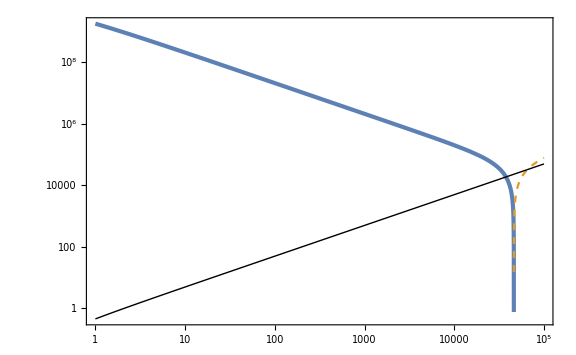

```mathematica
LogLogPlot[{ξΓinξg[ξg],-ξΓinξg[ξg],-ξΓmin[ξg]},{ξg,1,10^5},PlotStyle->{AbsoluteThickness[3],Dashed,{Thin,Black}}]
```

```mathematica
ξgs=10^5;
ξΓs=ξΓmin[ξgs];
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=500/Hin;
```

```mathematica
Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}//N
```

0.00365148

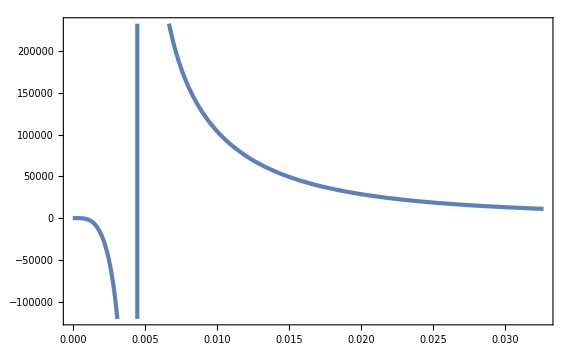

```mathematica
Plot[KK[x]/.{ξg->ξgs,ξΓ->ξΓs},{x,0,xin}]
```

```mathematica
χ[x_]:=NIntegrate[Sqrt[KK[xp]]/.{ξg->ξgs,ξΓ->ξΓs},{xp,0,x},WorkingPrecision->30];
```

```mathematica
χ[xin]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xp near {xp} = {0.00452886218611366257275370993543}. NIntegrate obtained 7.30872500973075681347684492748+1.54938059253313922862464637379 ⅈ and 0.191020197717880658031574211547 for the integral and error estimates.

7.30872500973075681347684492748+1.54938059253313922862464637379 ⅈ

```mathematica
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]]
```

{x[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],p[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],NN[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t],tinf[t]→                                                                                 7
InterpolatingFunction[{{0, 8.8226340716869073965425069157090282294074715964099 10 }}, <>][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
```

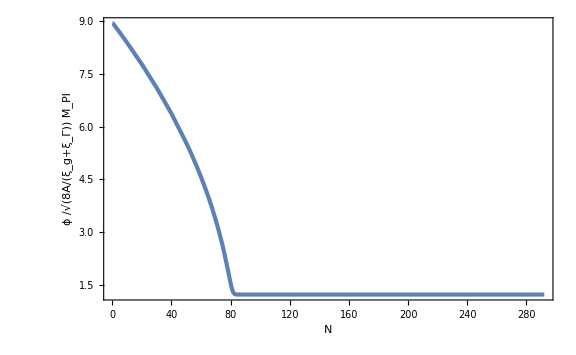

```mathematica
ParametricPlot[{Nsol[t],xsol[t]/Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{ϕ," /",Sqrt["8A/(ξ_g+ξ_Γ)"] Subscript[M, Pl]}]}]
```

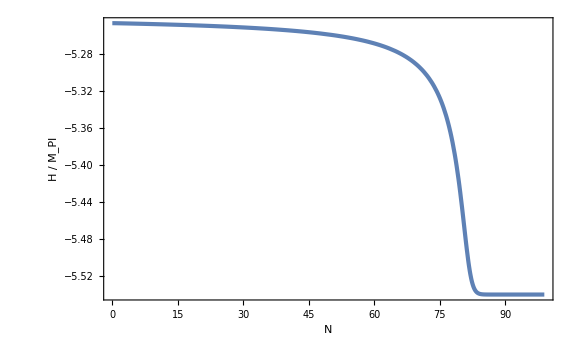

```mathematica
ParametricPlot[{Nsol[t],Log10[Hsol[t]]},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{H," / ",Subscript[M, Pl]}]}]
```

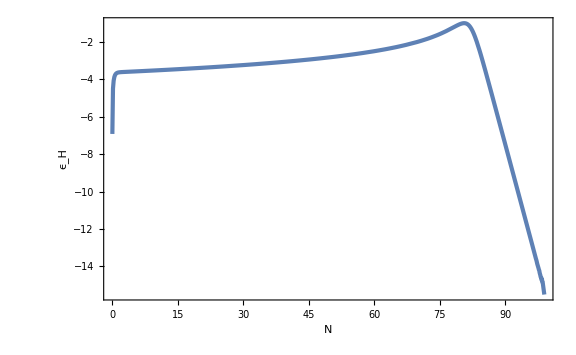

```mathematica
ParametricPlot[{Nsol[t],Log10[ϵHsol[t]]},{t,0,tf},FrameLabel->{N,Subscript[ϵ, H]}]
```

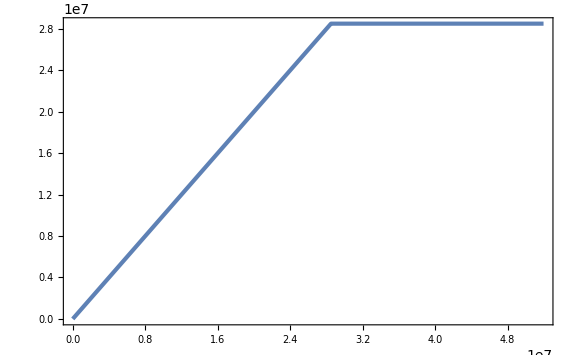

```mathematica
Plot[tinfsol[t],{t,0,tf}]
```

```mathematica
tend=tinfsol[tf]
Nend=Nsol[tend]
Ns=Nend-55
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30]
```

2.8501782309232901902760449448456241655729386127013×10^7

82.27751854029319594952016525230269800980543503249

27.27751854029319594952016525230269800980543503249

9.44921073789459862899288210613×10^6

```mathematica
tensor=16ϵVsol[ts]
ranal=(1+6ξg)/(ξg+ξΓ)2/NN^2/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

7.4937834402645943314043699537×10^-9

7.00826×10^-9

```mathematica
calP=1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs}
calPanal=1/((1+6ξg)(ξg+ξΓ))NN^2/(12 π^2)/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

0.00022534491230333370983536704152

0.000240956

```mathematica
nsm1=-6ϵVsol[ts]+2ηVsol[ts]
nsm1anal=-2/55//N
```

-0.037602149083014374523545393748

-0.0363636

### param. search

```mathematica
AbsoluteTiming[ξgs=10^0;ξΓs=10^4;
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=150/Hin;
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]];
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
tend=tinfsol[tf];
Nend=Nsol[tend];
Ns=Nend-55;
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30];
{1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs},1-6ϵVsol[ts]+2ηVsol[ts],16ϵVsol[ts]}]
```

{6.08852,{0.0003413722215886057460068634941,0.962407199750719008251393682127,4.9457543631613716154725551846×10^-7}}

```mathematica
calPnsrList=Table[ξgs=10^logξg;ξΓs=10^logξΓ;
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=150/Hin;
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]];
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
tend=tinfsol[tf];
Nend=Nsol[tend];
Ns=Nend-55;
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30];
{ξgs,ξΓs,1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs},1-6ϵVsol[ts]+2ηVsol[ts],16ϵVsol[ts]},{logξg,-2,5},{logξΓ,-2,10}];//AbsoluteTiming
```

{534.02,Null}

```mathematica
Export["calPnsr.dat",Flatten[calPnsrList,1]];
```

```mathematica
calPnsrList=Import["calPnsr.dat"]//ToExpression;
```

```mathematica
LogcalPList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]]}&,calPnsrList];
LogrList=Map[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[5]]]}&,calPnsrList];
nsList=Map[{Log10[#[[1]]],Log10[#[[2]]],#[[4]]}&,calPnsrList];
```

```mathematica
LogcalPint[logξg_,logξΓ_]=Interpolation[LogcalPList][logξg,logξΓ];
Logrint[logξg_,logξΓ_]=Interpolation[LogrList][logξg,logξΓ];
nsint[logξg_,logξΓ_]=Interpolation[nsList][logξg,logξΓ];
```

```mathematica
Clear[calPanal,ranal]
calPanal[ξg_,ξΓ_]=1/((1+6ξg)(ξg+ξΓ))55^2/(12 π^2);
ranal[ξg_,ξΓ_]=(1+6ξg)/(ξg+ξΓ)2/55^2;
```

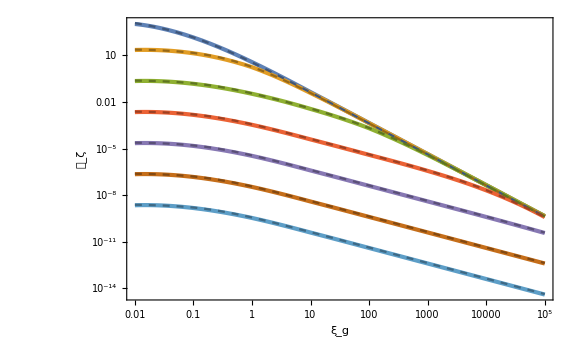

```mathematica
LogLogPlot[{10^LogcalPint[Log10[ξg],-2],10^LogcalPint[Log10[ξg],0],10^LogcalPint[Log10[ξg],2],10^LogcalPint[Log10[ξg],4],10^LogcalPint[Log10[ξg],6],10^LogcalPint[Log10[ξg],8],10^LogcalPint[Log10[ξg],10],calPanal[ξg,10^-2],calPanal[ξg,10^0],calPanal[ξg,10^2],calPanal[ξg,10^4],calPanal[ξg,10^6],calPanal[ξg,10^8],calPanal[ξg,10^10]},{ξg,10^-2,10^5},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Darker[Color[1]],Dashed},{Darker[Color[2]],Dashed},{Darker[Color[3]],Dashed},{Darker[Color[4]],Dashed},{Darker[Color[5]],Dashed},{Darker[Color[6]],Dashed},{Darker[Color[7]],Dashed}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

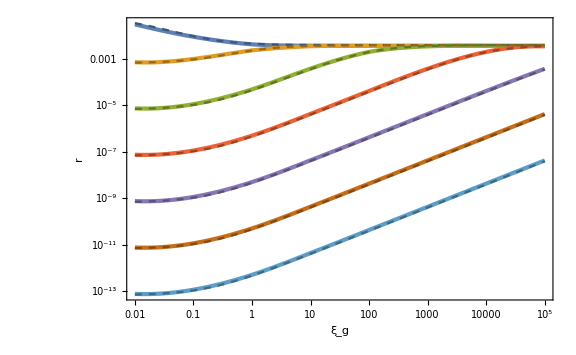

```mathematica
LogLogPlot[{10^Logrint[Log10[ξg],-2],10^Logrint[Log10[ξg],0],10^Logrint[Log10[ξg],2],10^Logrint[Log10[ξg],4],10^Logrint[Log10[ξg],6],10^Logrint[Log10[ξg],8],10^Logrint[Log10[ξg],10],ranal[ξg,10^-2],ranal[ξg,10^0],ranal[ξg,10^2],ranal[ξg,10^4],ranal[ξg,10^6],ranal[ξg,10^8],ranal[ξg,10^10]},{ξg,10^-2,10^5},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Darker[Color[1]],Dashed},{Darker[Color[2]],Dashed},{Darker[Color[3]],Dashed},{Darker[Color[4]],Dashed},{Darker[Color[5]],Dashed},{Darker[Color[6]],Dashed},{Darker[Color[7]],Dashed}},FrameLabel->{{r,None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

```mathematica
Clear[n]
```

```mathematica
nsanal[ξg_,ξΓ_]=1-2/55-6/(8AA 55^2)
```

53/55-3/(12100 √((ξg+ξΓ)/(1+6 ξg)))

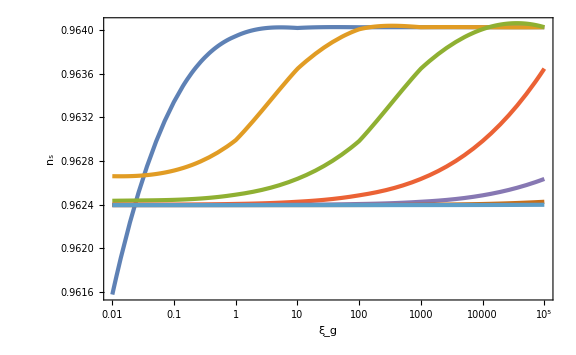

```mathematica
LogLinearPlot[{nsint[Log10[ξg],-2],nsint[Log10[ξg],0],nsint[Log10[ξg],2],nsint[Log10[ξg],4],nsint[Log10[ξg],6],nsint[Log10[ξg],8],nsint[Log10[ξg],10]},{ξg,10^-2,10^5},PlotRange->Full,GridLines->{None,{1-2/55}},FrameLabel->{{Subscript[n, "s"],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}}]
```

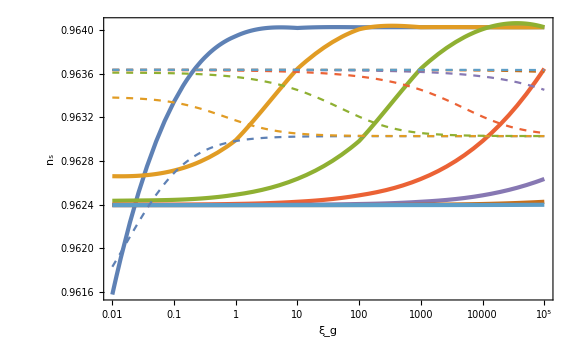

```mathematica
LogLinearPlot[{nsint[Log10[ξg],-2],nsint[Log10[ξg],0],nsint[Log10[ξg],2],nsint[Log10[ξg],4],nsint[Log10[ξg],6],nsint[Log10[ξg],8],nsint[Log10[ξg],10],nsanal[ξg,10^-2],nsanal[ξg,10^0],nsanal[ξg,10^2],nsanal[ξg,10^4],nsanal[ξg,10^6],nsanal[ξg,10^8],nsanal[ξg,10^10]},{ξg,10^-2,10^5},PlotRange->Full(*,GridLines->{None,{1-2/55}}*),FrameLabel->{{Subscript[n, "s"],None},{Subscript[ξ, g],Row[{λ==1,", ",N==55}]}},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dashed},{Color[2],Dashed},{Color[3],Dashed},{Color[4],Dashed},{Color[5],Dashed},{Color[6],Dashed},{Color[7],Dashed}}]
```

### sample lin. ptb.

```mathematica
ξΓinξg[ξg_]=ξΓ/.Solve[1/((1+6ξg)(ξg+ξΓ))55^2/(12 π^2)==2 10^-9,ξΓ][[1]]
```

(378125000000-3 π^2 ξg-18 π^2 ξg^2)/(3 π^2 (1+6 ξg))

```mathematica
ξΓmin[10^3]
```

-5999000/11999

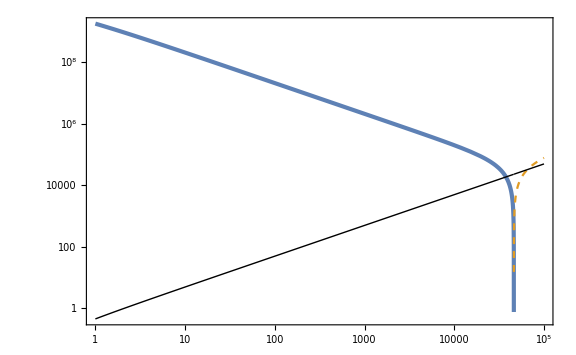

```mathematica
LogLogPlot[{ξΓinξg[ξg],-ξΓinξg[ξg],-ξΓmin[ξg]},{ξg,1,10^5},PlotStyle->{AbsoluteThickness[3],Dashed,{Thin,Black}}]
```

```mathematica
ξgs=10^4;
ξΓs=ξΓmin[ξgs];
xin=Sqrt[(8 AA^2)/(ξg+ξΓ)NN]/.{ξg->ξgs,ξΓ->ξΓs,NN->80};
Hin=HH[xin,0]/.{ξg->ξgs,ξΓ->ξΓs};
tf=500/Hin;
```

```mathematica
Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}//N
```

0.0115469

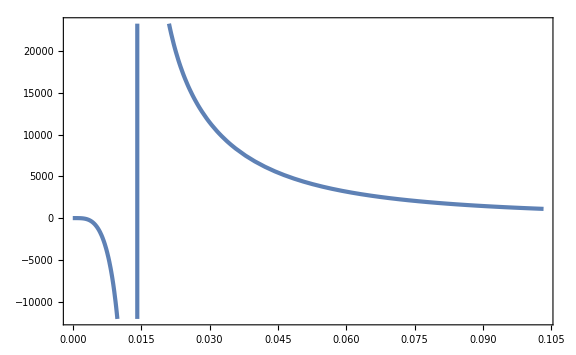

```mathematica
Plot[KK[x]/.{ξg->ξgs,ξΓ->ξΓs},{x,0,xin}]
```

```mathematica
χ[x_]:=NIntegrate[Sqrt[KK[xp]]/.{ξg->ξgs,ξΓ->ξΓs},{xp,0,x},WorkingPrecision->30];
```

```mathematica
χ[xin]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xp near {xp} = {0.0143214123071180634918397416885}. NIntegrate obtained 7.5510317745873074153513534625+1.54789874337378875353922877037 ⅈ and 0.431541123002736252644670322068 for the integral and error estimates.

7.5510317745873074153513534625+1.54789874337378875353922877037 ⅈ

```mathematica
sol=NDSolve[{x'[t]==UnitStep[1-ϵH[x[t],p[t]]]p[t],
p'[t]==-UnitStep[1-ϵH[x[t],p[t]]]((3HH[x[t],p[t]]+KK'[x[t]]/(2KK[x[t]])p[t])p[t]+VV'[x[t]]/KK[x[t]]),
x[0]==xin,p[0]==0,
NN'[t]==HH[x[t],p[t]],NN[0]==0,
tinf'[t]==UnitStep[1-ϵH[x[t],p[t]]],tinf[0]==0}/.{ξg->ξgs,ξΓ->ξΓs},{x[t],p[t],NN[t],tinf[t]},{t,0,tf},WorkingPrecision->50,MaxSteps->100000][[1]]
```

{x[t]→                                                                                 6
InterpolatingFunction[{{0, 8.8227086767684157856654761595715161423071957825169 10 }}, <>][t],p[t]→                                                                                 6
InterpolatingFunction[{{0, 8.8227086767684157856654761595715161423071957825169 10 }}, <>][t],NN[t]→                                                                                 6
InterpolatingFunction[{{0, 8.8227086767684157856654761595715161423071957825169 10 }}, <>][t],tinf[t]→                                                                                 6
InterpolatingFunction[{{0, 8.8227086767684157856654761595715161423071957825169 10 }}, <>][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=p[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=HH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
Hdotsol[t_]=-(KK[xsol[t]] psol[t]^2)/2/.{ξg->ξgs,ξΓ->ξΓs};
Hddotsol[t_]=KK[xsol[t]]psol[t](3Hsol[t]psol[t]+VV'[xsol[t]]/KK[xsol[t]])/.{ξg->ξgs,ξΓ->ξΓs};
ϵHsol[t_]=ϵH[xsol[t],psol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ϵVsol[t_]=ϵV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
ηVsol[t_]=ηV[xsol[t]]/.{ξg->ξgs,ξΓ->ξΓs};
tinfsol[t_]=tinf[t]/.sol;
```

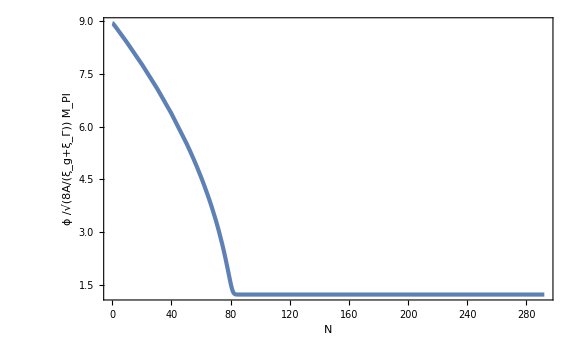

```mathematica
ParametricPlot[{Nsol[t],xsol[t]/Sqrt[(8 AA^2)/(ξg+ξΓ)]/.{ξg->ξgs,ξΓ->ξΓs}},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{ϕ," /",Sqrt["8A/(ξ_g+ξ_Γ)"] Subscript[M, Pl]}]}]
```

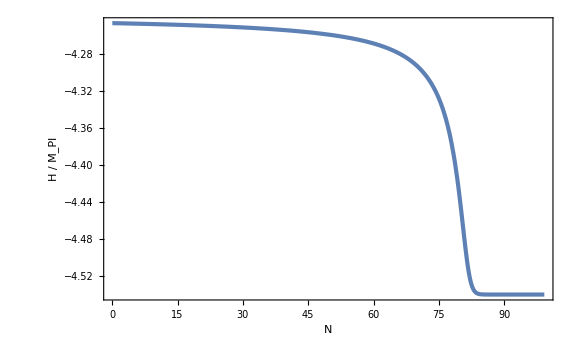

```mathematica
ParametricPlot[{Nsol[t],Log10[Hsol[t]]},{t,0,tf},PlotRange->Full,FrameLabel->{N,Row[{H," / ",Subscript[M, Pl]}]}]
```

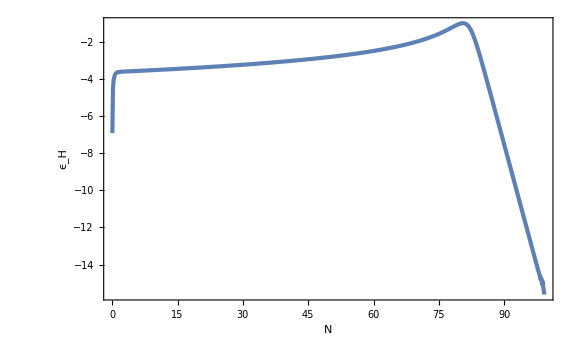

```mathematica
ParametricPlot[{Nsol[t],Log10[ϵHsol[t]]},{t,0,tf},FrameLabel->{N,Subscript[ϵ, H]}]
```

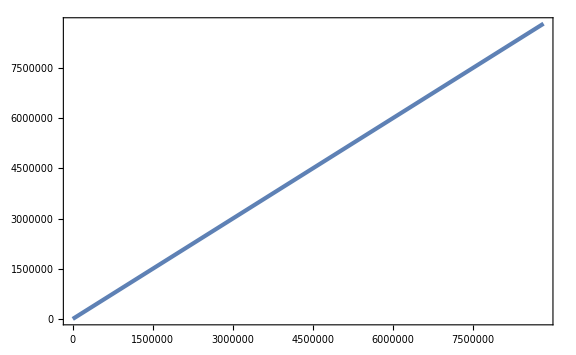

```mathematica
Plot[tinfsol[t],{t,0,tf}]
```

```mathematica
tend=tinfsol[tf]
Nend=Nsol[tend]
Ns=Nend-55
ts=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30]
```

8.822708676768415785665476159571516142307195782517×10^6

292.1188435440422952294097814129168870951141815613

237.1188435440422952294097814129168870951141815613

6.91745278844265076278528518392×10^6

```mathematica
coord={x};
n=Length[coord];
metric={{K[x]}};
inversemetric=Inverse[metric];
```

```mathematica
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | K'[x]/(2 K[x])

```mathematica
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

{}

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

{}

```mathematica
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify
```

0

```mathematica
DN=7;
```

```mathematica
Ni=Ns-DN;
ti=t/.FindRoot[Nsol[t]==Ns,{t,1/4 tf},WorkingPrecision->30];
```

```mathematica
ks=Exp[Ns]Hsol[ts]
```

2.753053704933314707633850638934793831465919452×10^98

```mathematica
ptbsol=NDSolve[]
```

```mathematica
tensor=16ϵVsol[ts]
ranal=(1+6ξg)/(ξg+ξΓ)2/NN^2/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

7.4937834402645943314043699537×10^-9

7.00826×10^-9

```mathematica
calP=1/(24 π^2)VV[xsol[ts]]/ϵVsol[ts]/.{ξg->ξgs,ξΓ->ξΓs}
calPanal=1/((1+6ξg)(ξg+ξΓ))NN^2/(12 π^2)/.{ξg->ξgs,ξΓ->ξΓs,NN->55}//N
```

0.00022534491230333370983536704152

0.000240956

```mathematica
nsm1=-6ϵVsol[ts]+2ηVsol[ts]
nsm1anal=-2/55//N
```

-0.037602149083014374523545393748

-0.0363636

## metric w/ EH

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
metric=1/((1+(ξg+ξΓ)Sum[coord[[i]]^2,{i,n}]/Mp^2)^2)1/(MΓ^2+ξΓ Sum[coord[[i]]^2,{i,n}])Table[(1+(ξg+ξΓ)Sum[coord[[s]]^2,{s,n}]/Mp^2)(MΓ^2+ξΓ Sum[coord[[s]]^2,{s,n}])KroneckerDelta[i,j]+6((MΓ^2/Mp^2-1)ξΓ^2+ξg(2ξΓ+ξg)MΓ^2/Mp^2+ξΓ ξg(ξg+ξΓ)Sum[coord[[s]]^2,{s,n}]/Mp^2)coord[[i]]coord[[j]],{i,n},{j,n}]//Simplify
```

{{(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h1^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h1 h2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h1 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h1 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h2^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h2 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h3 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h3^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2),(6 h3 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2)},{(6 h1 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h2 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(6 h3 h4 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/((MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp)^2),(1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2+(6 h4^2 (-((Mp^2-MΓ^2) ξΓ^2)+(h1^2+h2^2+h3^2+h4^2) ξg ξΓ (ξg+ξΓ)+MΓ^2 ξg (ξg+2 ξΓ)))/(Mp^2 (MΓ^2+(h1^2+h2^2+h3^2+h4^2) ξΓ)))/((1+((h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))/Mp^2)^2)}}

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (Mp^2 (MΓ^2+ξΓ (h1^2-(h2^2+h3^2+h4^2) (-1+6 ξΓ)))+(ξg+ξΓ) (h1^4 ξΓ+h1^2 (MΓ^2+2 (h2^2+h3^2+h4^2) (1+3 ξg) ξΓ)+(h2^2+h3^2+h4^2) ((h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))),-((6 h1 h2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h1 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h1 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h2 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h1^2 (1-6 ξΓ)-(h3^2+h4^2) (-1+6 ξΓ)))-(ξg+ξΓ) (h2^4 ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^2 (MΓ^2+2 (h3^2+h4^2) (1+3 ξg) ξΓ)+(h3^2+h4^2) ((h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2 (1+3 ξg)+(h3^2+h4^2) (1+6 ξg)) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h3 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h3^2+h4^2+h1^2 (1-6 ξΓ)-6 h2^2 ξΓ-6 h4^2 ξΓ))-(ξg+ξΓ) (h3^2 MΓ^2+h4^2 MΓ^2+6 h4^2 MΓ^2 ξg+h3^4 ξΓ+2 h3^2 h4^2 ξΓ+h4^4 ξΓ+6 h4^2 MΓ^2 ξΓ+6 h3^2 h4^2 ξg ξΓ+6 h4^4 ξg ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^4 (ξΓ+6 ξg ξΓ)+h2^2 (2 (h3^2+h4^2+3 h3^2 ξg+6 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2+h3^2+h4^2+6 h2^2 ξg+3 h3^2 ξg+6 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h3 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))},{-((6 h1 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h2 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-((6 h3 h4 (Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (MΓ^2 (ξg+ξΓ)^2+ξΓ (h3^2 ξg^2+h4^2 ξg^2-Mp^2 ξΓ+h3^2 ξg ξΓ+h4^2 ξg ξΓ+h1^2 ξg (ξg+ξΓ)+h2^2 ξg (ξg+ξΓ))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))),-(((Mp^2+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)) (-Mp^2 (MΓ^2+ξΓ (h2^2+h3^2+h4^2+h1^2 (1-6 ξΓ)-6 h2^2 ξΓ-6 h3^2 ξΓ))-(ξg+ξΓ) (h3^2 MΓ^2+h4^2 MΓ^2+6 h3^2 MΓ^2 ξg+h3^4 ξΓ+2 h3^2 h4^2 ξΓ+h4^4 ξΓ+6 h3^2 MΓ^2 ξΓ+6 h3^4 ξg ξΓ+6 h3^2 h4^2 ξg ξΓ+h1^4 (ξΓ+6 ξg ξΓ)+h2^4 (ξΓ+6 ξg ξΓ)+h2^2 (2 (h3^2+h4^2+6 h3^2 ξg+3 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))+h1^2 (2 (h2^2+h3^2+h4^2+6 h2^2 ξg+6 h3^2 ξg+3 h4^2 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))))/(Mp^4 (MΓ^2-(h1^2+h2^2+h3^2+h4^2) ξΓ (-1+6 ξΓ))+(h1^2+h2^2+h3^2+h4^2) Mp^2 (ξg+ξΓ) ((h1^2+h2^2+h3^2+h4^2) (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))))}}

```mathematica
Clear[affine]
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
Clear[riemann]
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

1
 |  |  |  |

```mathematica
Clear[scalar]
scalar[h_]=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify(*/.{h1^2->h^2-h2^2-h3^2-h4^2,h1^4->(h^2-h2^2-h3^2-h4^2)^2,h1^6->(h^2-h2^2-h3^2-h4^2)^3,h1^8->(h^2-h2^2-h3^2-h4^2)^4}*)
```

(6 (-6 Mp^6 ξΓ^2 (2 MΓ^2+h^2 (1-6 ξΓ) ξΓ)+h^4 (ξg+ξΓ)^3 (h^2 (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ))^2+h^2 Mp^2 (ξg+ξΓ)^2 (h^4 (1+6 ξg) (5+6 ξg-12 ξΓ) ξΓ^2+2 h^2 MΓ^2 ξΓ (5+36 ξg+36 ξg^2+9 ξΓ-36 ξΓ^2)+MΓ^4 (5+36 ξg^2+36 ξΓ+36 ξΓ^2+36 ξg (1+2 ξΓ)))+2 Mp^4 (2 MΓ^4 (ξg+3 ξg^2+ξΓ+6 ξg ξΓ+3 ξΓ^2)-h^4 ξΓ^2 (-1+6 ξΓ) (6 ξg^2+(2-3 ξΓ) ξΓ+ξg (2+3 ξΓ))-h^2 MΓ^2 ξΓ (12 ξg^2 (-1+3 ξΓ)+ξΓ (-4+15 ξΓ+36 ξΓ^2)+ξg (-4+3 ξΓ+72 ξΓ^2)))))/(Mp^3 (MΓ^2+h^2 (1-6 ξΓ) ξΓ)+h^2 Mp (ξg+ξΓ) (h^2 (1+6 ξg) ξΓ+MΓ^2 (1+6 ξg+6 ξΓ)))^2

```mathematica
Mp^2 scalar[x Mp]/.{MΓ^2->f^2 Mp^2,MΓ^4->f^4 Mp^4}//FullSimplify
```

$Aborted

```mathematica
x2pole1=x2/.Solve[x2 ξΓ (1-6 ξΓ+x2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))==0,x2][[1]]//Simplify
x2pole2=x2/.Solve[x2 ξΓ (1-6 ξΓ+x2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))==0,x2][[2]]//Simplify
```

-(f^2 ξg+6 f^2 ξg^2+ξΓ+f^2 ξΓ+12 f^2 ξg ξΓ-6 ξΓ^2+6 f^2 ξΓ^2+√(-4 f^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(ξΓ-6 ξΓ^2+f^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2))^2))/(2 (1+6 ξg) ξΓ (ξg+ξΓ))

-(f^2 ξg+6 f^2 ξg^2+ξΓ+f^2 ξΓ+12 f^2 ξg ξΓ-6 ξΓ^2+6 f^2 ξΓ^2-√(-4 f^2 (1+6 ξg) ξΓ (ξg+ξΓ)+(ξΓ-6 ξΓ^2+f^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2))^2))/(2 (1+6 ξg) ξΓ (ξg+ξΓ))

```mathematica
Collect[x2 ξΓ (1-6 ξΓ+x2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x2 (ξg+ξΓ) (1+6 ξg+6 ξΓ)),x2,Simplify]
```

f^2+x2^2 (1+6 ξg) ξΓ (ξg+ξΓ)+x2 (ξΓ-6 ξΓ^2+f^2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))

```mathematica
(ξΓ-6 ξΓ^2+f^2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))-4 f^2(1+6 ξg) ξΓ (ξg+ξΓ)//FullSimplify
```

ξΓ-6 ξΓ^2-f^2 (ξg+ξΓ) (-1-2 ξΓ+6 ξg (-1+4 ξΓ))

```mathematica
x2pole1/.{f->0.6,ξg->100,ξΓ->200}
x2pole2/.{f->0.6,ξg->100,ξΓ->200}
```

7.99937×10^-6

0.00124802

```mathematica
Collect[(6 (4 f^4 (ξg+ξΓ) (1+3 ξg+3 ξΓ)-2 x^4 (2+6 ξg-3 ξΓ) ξΓ^2 (ξg+ξΓ) (-1+6 ξΓ)-6 ξΓ^2 (2 f^2+x^2 (1-6 ξΓ) ξΓ)+x^4 (ξg+ξΓ)^3 (x^2 (1+6 ξg) ξΓ+f^2 (1+6 ξg+6 ξΓ))^2-2 f^2 x^2 ξΓ (ξg+ξΓ) (-4+12 ξg (-1+3 ξΓ)+3 ξΓ (5+12 ξΓ))+x^2 (ξg+ξΓ)^2 (x^4 (1+6 ξg) (5+6 ξg-12 ξΓ) ξΓ^2+f^4 (1+6 ξg+6 ξΓ) (5+6 ξg+6 ξΓ)+2 f^2 x^2 ξΓ (5+36 ξg (1+ξg)+9 (1-4 ξΓ) ξΓ)))),x,Simplify]
```

-72 f^2 ξΓ^2+24 f^4 (ξg+ξΓ) (1+3 ξg+3 ξΓ)+6 x^8 (ξg+ξΓ)^3 (ξΓ+6 ξg ξΓ)^2+6 x^6 (1+6 ξg) ξΓ (ξg+ξΓ)^2 ((5+6 ξg-12 ξΓ) ξΓ+2 f^2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))+6 x^4 (ξg+ξΓ) (-2 (2+6 ξg-3 ξΓ) ξΓ^2 (-1+6 ξΓ)+f^4 (ξg+ξΓ)^2 (1+6 ξg+6 ξΓ)^2+2 f^2 ξΓ (ξg+ξΓ) (5+36 ξg (1+ξg)+9 (1-4 ξΓ) ξΓ))+6 x^2 (6 ξΓ^3 (-1+6 ξΓ)+f^4 (ξg+ξΓ)^2 (1+6 ξg+6 ξΓ) (5+6 ξg+6 ξΓ)-2 f^2 ξΓ (ξg+ξΓ) (-4+12 ξg (-1+3 ξΓ)+3 ξΓ (5+12 ξΓ)))

```mathematica
Collect[x^2 ξΓ (1-6 ξΓ+x^2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x^2 (ξg+ξΓ) (1+6 ξg+6 ξΓ)),x,Simplify]
```

f^2+x^4 (1+6 ξg) ξΓ (ξg+ξΓ)+x^2 (ξΓ-6 ξΓ^2+f^2 (ξg+ξΓ) (1+6 ξg+6 ξΓ))

```mathematica
scalar[0]//FullSimplify
```

-(72 ξΓ^2)/MΓ^2+(24 (ξg+ξΓ) (1+3 ξg+3 ξΓ))/Mp^2

```mathematica
scalar[h]-(6 (h^8 (ξg+ξΓ)^3 (ξΓ+6 ξg ξΓ)^2+4 Mp^8 (ξg+3 ξg^2+ξΓ+6 ξg ξΓ)+h^2 Mp^6 (1+6 ξg) (6 ξg^3+13 ξΓ^2+6 ξg ξΓ (3+4 ξΓ)+ξg^2 (5+24 ξΓ))+h^6 Mp^2 (1+6 ξg) ξΓ (ξg+ξΓ)^2 (12 ξg^2+7 ξΓ+ξg (2+30 ξΓ))+h^4 Mp^4 (1+6 ξg) (6 ξg^4+15 ξΓ^3+3 ξg ξΓ^2 (9+16 ξΓ)+ξg^3 (1+42 ξΓ)+ξg^2 ξΓ (13+84 ξΓ))))/(Mp^5+h^4 Mp (1+6 ξg) ξΓ (ξg+ξΓ)+h^2 Mp^3 (1+6 ξg) (ξg+2 ξΓ))^2/.{MΓ->Mp}//Simplify
```

0

```mathematica
Normal[Series[scalar[h],{h,∞,0}]]
```

(6 (ξg+ξΓ))/Mp^2

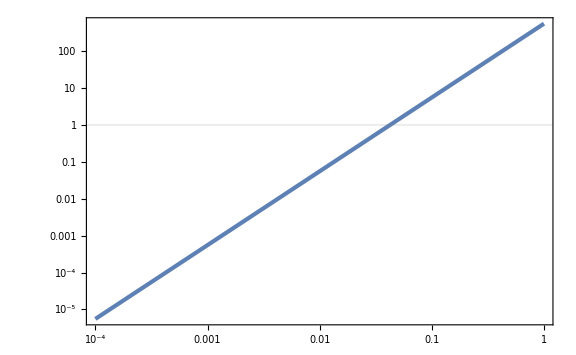

```mathematica
LogLogPlot[ξΓ h^2/MΓ^2/.{Mp->1,MΓ->0.6,ξg->100,ξΓ->200},{h,10^-4,1},GridLines->{None,{1}}]
```

```mathematica
hpole=h/.FindRoot[ξΓ h^2/MΓ^2==1/Sqrt[6]/.{Mp->1,MΓ->0.6,ξg->100,ξΓ->200},{h,0.1}]
```

0.0271081

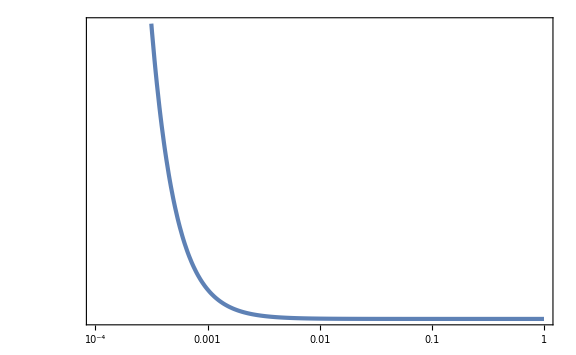

```mathematica
LogLogPlot[{scalar[h]/.{Mp->1,MΓ->0,ξg->100,ξΓ->10^9},-scalar[h]/.{Mp->1,MΓ->0,ξg->100,ξΓ->10^9}},{h,10^-4,1}(*,GridLines->{{Sqrt[x2pole1]/.{f->0.6,ξg->100,ξΓ->10^9},Sqrt[x2pole2]/.{f->0.6,ξg->100,ξΓ->10^9}},None}*)]
```

```mathematica
Eigenvalues[metric]/.{h2->0,h3->0,h4->0,h1->h}/.{MΓ->f Mp,h->x Mp}//Simplify
```

{1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),1/(1+x^2 (ξg+ξΓ)),(x^2 ξΓ (1-6 ξΓ+x^2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2)))/((f^2+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)}

```mathematica
F2[x_]=Eigenvalues[metric][[4]]/.{h2->0,h3->0,h4->0,h1->h}/.{MΓ->f Mp,h->x Mp}//Simplify
r[x_]=x Mp Sqrt[Eigenvalues[metric][[1]]/.{h2->0,h3->0,h4->0,h1->h}/.{MΓ->f Mp,h->x Mp}//Simplify]
```

(x^2 ξΓ (1-6 ξΓ+x^2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2)))/((f^2+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^2)

Mp x √(1/(1+x^2 (ξg+ξΓ)))

```mathematica
dzdr2[x_]=F2[x]-r'[x]^2/Mp^2//Simplify
```

(x^2 (ξΓ (-6 ξΓ+x^4 (1+6 ξg) (ξg+ξΓ)^2+2 x^2 (ξg+3 ξg^2+ξΓ-3 ξΓ^2))+f^2 (ξg+ξΓ) (2+6 x^2 ξg^2+(6+x^2) ξΓ+6 x^2 ξΓ^2+ξg (6+x^2 (1+12 ξΓ)))))/((f^2+x^2 ξΓ) (1+x^2 (ξg+ξΓ))^3)

```mathematica
-(f^2+x^2 ξΓ)+(1+x^2 (ξg+ξΓ)) (x^2 ξΓ (1-6 ξΓ+x^2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2)))//Simplify
```

-f^2-x^2 ξΓ+(1+x^2 (ξg+ξΓ)) (x^2 ξΓ (1-6 ξΓ+x^2 (1+6 ξg) (ξg+ξΓ))+f^2 (1+x^2 (ξg+6 ξg^2+ξΓ+12 ξg ξΓ+6 ξΓ^2)))

```mathematica
Normal[Series[dzdr2[x],{x,0,2}]]/.{ξg->0}//Simplify
```

(2 x^2 ξΓ (-3 ξΓ+f^2 (1+3 ξΓ)))/f^2

```mathematica
Normal[Series[F2[x],{x,0,2}]]/.{ξg->0}//Simplify
```

1+x^2 ξΓ (-1+(6-6/f^2) ξΓ)

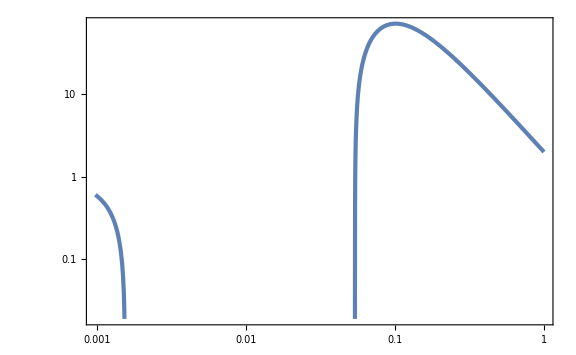

```mathematica
LogLogPlot[F2[x]/.{f->1/2,ξg->100,ξΓ->200},{x,0,1}]
```

## spherical coord

```mathematica
coord={r,t1,t2,t3};
n=Length[coord];
```

```mathematica
x=r Cos[t1];
y=r Sin[t1]Cos[t2];
z=r Sin[t1]Sin[t2]Cos[t3]
w=r Sin[t1]Sin[t2]Sin[t3];
xcoord={x,y,z,w};
```

r Cos[t3] Sin[t1] Sin[t2]

```mathematica
xcoord.Transpose[xcoord]//Simplify
```

r^2

```mathematica
dt={0,dt1,dt2,dt3};
dx=Table[Sum[dt[[s]]D[xcoord[[i]], coord[[s]]],{s,n}],{i,n}]//Simplify
```

{-dt1 r Sin[t1],r (dt1 Cos[t1] Cos[t2]-dt2 Sin[t1] Sin[t2]),r (dt2 Cos[t2] Cos[t3] Sin[t1]+Sin[t2] (dt1 Cos[t1] Cos[t3]-dt3 Sin[t1] Sin[t3])),r (dt3 Cos[t3] Sin[t1] Sin[t2]+(dt2 Cos[t2] Sin[t1]+dt1 Cos[t1] Sin[t2]) Sin[t3])}

```mathematica
dOmega=Collect[Transpose[dx].dx,Drop[dt,1],Simplify]/r^2//Simplify
```

dt1^2+Sin[t1]^2 (dt2^2+dt3^2 Sin[t2]^2)

```mathematica
ds2=F[r]^2 dr^2+rho[r]^2 dOmega
```

dr^2 F[r]^2+rho[r]^2 (dt1^2+Sin[t1]^2 (dt2^2+dt3^2 Sin[t2]^2))

```mathematica
dcoord={dr,dt1,dt2,dt3};
metric=Table[D[D[ds2, dcoord[[j]]], dcoord[[i]]],{i,n},{j,n}]//Simplify;metric//MatrixForm
```

(2 F[r]^2 | 0 | 0 | 0
0 | 2 rho[r]^2 | 0 | 0
0 | 0 | 2 rho[r]^2 Sin[t1]^2 | 0
0 | 0 | 0 | 2 rho[r]^2 Sin[t1]^2 Sin[t2]^2)

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{1/(2 F[r]^2),0,0,0},{0,1/(2 rho[r]^2),0,0},{0,0,Csc[t1]^2/(2 rho[r]^2),0},{0,0,0,(Csc[t1]^2 Csc[t2]^2)/(2 rho[r]^2)}}

```mathematica
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | F'[r]/F[r]
Γ[1, 2, 2] | -(rho[r] rho'[r])/F[r]^2
Γ[1, 3, 3] | -(rho[r] Sin[t1]^2 rho'[r])/F[r]^2
Γ[1, 4, 4] | -(rho[r] Sin[t1]^2 Sin[t2]^2 rho'[r])/F[r]^2
Γ[2, 2, 1] | rho'[r]/rho[r]
Γ[2, 3, 3] | -Cos[t1] Sin[t1]
Γ[2, 4, 4] | -Cos[t1] Sin[t1] Sin[t2]^2
Γ[3, 3, 1] | rho'[r]/rho[r]
Γ[3, 3, 2] | Cot[t1]
Γ[3, 4, 4] | -Cos[t2] Sin[t2]
Γ[4, 4, 1] | rho'[r]/rho[r]
Γ[4, 4, 2] | Cot[t1]
Γ[4, 4, 3] | Cot[t2]

```mathematica
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(rho[r] F'[r] rho'[r])/F[r]^3+(rho[r] rho''[r])/F[r]^2
R[1, 3, 3, 1] | -(rho[r] Sin[t1]^2 F'[r] rho'[r])/F[r]^3+(rho[r] Sin[t1]^2 rho''[r])/F[r]^2
R[1, 4, 4, 1] | -(rho[r] Sin[t1]^2 Sin[t2]^2 F'[r] rho'[r])/F[r]^3+(rho[r] Sin[t1]^2 Sin[t2]^2 rho''[r])/F[r]^2
R[2, 1, 2, 1] | (F'[r] rho'[r])/(F[r] rho[r])-rho''[r]/rho[r]
R[2, 3, 3, 2] | -Sin[t1]^2+(Sin[t1]^2 rho'[r]^2)/F[r]^2
R[2, 4, 4, 2] | -Sin[t1]^2 Sin[t2]^2+(Sin[t1]^2 Sin[t2]^2 rho'[r]^2)/F[r]^2
R[3, 1, 3, 1] | (F'[r] rho'[r])/(F[r] rho[r])-rho''[r]/rho[r]
R[3, 2, 3, 2] | -Cot[t1]^2+Csc[t1]^2-rho'[r]^2/F[r]^2
R[3, 4, 4, 3] | -Sin[t2]^2+Cos[t1]^2 Sin[t2]^2+(Sin[t1]^2 Sin[t2]^2 rho'[r]^2)/F[r]^2
R[4, 1, 4, 1] | (F'[r] rho'[r])/(F[r] rho[r])-rho''[r]/rho[r]
R[4, 2, 4, 2] | -Cot[t1]^2+Csc[t1]^2-rho'[r]^2/F[r]^2
R[4, 3, 4, 3] | -Cos[t1]^2-Cot[t2]^2+Csc[t2]^2-(Sin[t1]^2 rho'[r]^2)/F[r]^2

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | (3 F'[r] rho'[r])/(F[r] rho[r])-(3 rho''[r])/rho[r]
R[2, 2] | -2 Cot[t1]^2+2 Csc[t1]^2+(rho[r] F'[r] rho'[r])/F[r]^3-(2 rho'[r]^2)/F[r]^2-(rho[r] rho''[r])/F[r]^2
R[3, 3] | -Cos[t1]^2-Cot[t2]^2+Csc[t2]^2+Sin[t1]^2+(rho[r] Sin[t1]^2 F'[r] rho'[r])/F[r]^3-(2 Sin[t1]^2 rho'[r]^2)/F[r]^2-(rho[r] Sin[t1]^2 rho''[r])/F[r]^2
R[4, 4] | Sin[t2]^2-Cos[t1]^2 Sin[t2]^2+Sin[t1]^2 Sin[t2]^2+(rho[r] Sin[t1]^2 Sin[t2]^2 F'[r] rho'[r])/F[r]^3-(2 Sin[t1]^2 Sin[t2]^2 rho'[r]^2)/F[r]^2-(rho[r] Sin[t1]^2 Sin[t2]^2 rho''[r])/F[r]^2

```mathematica
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]//Simplify
```

(3 (F[r]^3+rho[r] F'[r] rho'[r]-F[r] (rho'[r]^2+rho[r] rho''[r])))/(F[r]^3 rho[r]^2)

```mathematica
Normal[Series[scalar/.{F[r]->1+A r^2,F'[r]->2A r,rho[r]->r(1+B r^2),rho'[r]->1+3B r^2,rho''[r]->6B r},{r,0,2}]]
```

12 (A-3 B)-9 (3 A^2-8 A B-3 B^2) r^2

```mathematica
Normal[Series[F[r]^2-rho'[r]^2/.{F[r]->1+A r^2,rho'[r]->1+3B r^2},{r,0,2}]]
```

(2 A-6 B) r^2

```mathematica
D[D[Sqrt[r^2/(1+a r^2)], r], r]//Simplify
```

-(3 a √(r^2/(1+a r^2)))/((1+a r^2)^2)

```mathematica
(D[Sqrt[r^2/(1+a r^2)], r])^2+Sqrt[r^2/(1+a r^2)]D[D[Sqrt[r^2/(1+a r^2)], r], r]//Simplify
```

(1-3 a r^2)/((1+a r^2)^3)

```mathematica
scalar/.{rho[r]->Sqrt[r^2/(1+a r^2)],rho'[r]->D[Sqrt[r^2/(1+a r^2)], r],rho''[r]->D[D[Sqrt[r^2/(1+a r^2)], r], r]}//Simplify
```

(3 ((-1+3 a r^2) F[r]+(1+a r^2)^3 F[r]^3+r (1+a r^2) F'[r]))/((r+a r^3)^2 F[r]^3)

## embedding

```mathematica
coord={h1,h2,h3,h4};
n=Length[coord];
```

```mathematica
metric=IdentityMatrix[n]/(1+(ξg/δ+ξΓ/δ)(coord.coord)/Mp^2)+(6 ξg/δ(2 ξΓ/δ+ξg/δ+ξΓ/δ(ξΓ/δ+ξg/δ)(coord.coord)/Mp^2))/((1+ξΓ/δ (coord.coord)/Mp^2)(1+(ξg/δ+ξΓ/δ)(coord.coord)/Mp^2)^2)Table[(coord[[i]]coord[[j]])/Mp^2,{i,n},{j,n}]//Simplify;
```

```mathematica
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
affine:=affine=Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

```mathematica
riemann:=riemann=Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

```mathematica
ricci:=ricci=Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

```mathematica
scalar=Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]/.{h2->0,h3->0,h4->0,h1->h}//Simplify
```

(6 (h^8 (δ+6 ξg)^2 ξΓ^2 (ξg+ξΓ)^3+4 Mp^8 δ^5 (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ))+h^6 Mp^2 δ (δ+6 ξg) ξΓ (ξg+ξΓ)^2 (6 ξg (2 ξg+5 ξΓ)+δ (2 ξg+7 ξΓ))+h^2 Mp^6 δ^3 (δ+6 ξg) (6 ξg (ξg+2 ξΓ)^2+δ (5 ξg^2+18 ξg ξΓ+13 ξΓ^2))+h^4 Mp^4 δ^2 (δ+6 ξg) (ξg+ξΓ) (6 ξg (ξg^2+6 ξg ξΓ+8 ξΓ^2)+δ (ξg^2+12 ξg ξΓ+15 ξΓ^2))))/(δ (Mp^5 δ^3+h^4 Mp (δ+6 ξg) ξΓ (ξg+ξΓ)+h^2 Mp^3 δ (δ+6 ξg) (ξg+2 ξΓ))^2)

```mathematica
Normal[Series[scalar,{h,∞,0}]]
```

(6 (ξg+ξΓ))/(Mp^2 δ)

```mathematica
scalar/.{h->0}
```

(24 (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ)))/(Mp^2 δ^2)

```mathematica
Λorigin[ξg_,ξΓ_]=(Mp^2 scalar/.{h->0,δ->1})^(-1/2)
```

1/(2 √6 √(ξg+ξΓ+3 ξg (ξg+2 ξΓ)))

```mathematica
Eigenvalues[metric]//Simplify
```

{(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^2 δ)/(Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ)),(Mp^6 δ^3+(h1^2+h2^2+h3^2+h4^2)^2 Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ)+(h1^2+h2^2+h3^2+h4^2) Mp^4 δ (δ+6 ξg) (ξg+2 ξΓ))/((Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) ξΓ) (Mp^2 δ+(h1^2+h2^2+h3^2+h4^2) (ξg+ξΓ))^2)}

```mathematica
F2[ρJ_]=Eigenvalues[metric][[4]]/.{h2->0,h3->0,h4->0,h1->ρJ}//Simplify
ρinρJ[ρJ_]=Simplify[Sqrt[ρJ^2 Eigenvalues[metric][[1]]/.{h2->0,h3->0,h4->0,h1->ρJ}],{ρJ>0,Mp>0}]
```

(Mp^6 δ^3+Mp^4 δ (δ+6 ξg) (ξg+2 ξΓ) ρJ^2+Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ) ρJ^4)/((Mp^2 δ+ξΓ ρJ^2) (Mp^2 δ+(ξg+ξΓ) ρJ^2)^2)

Mp ρJ √(δ/(Mp^2 δ+(ξg+ξΓ) ρJ^2))

```mathematica
int[ρJ_]=Simplify[Sqrt[F2[ρJ]-ρinρJ'[ρJ]^2],{Mp>0,ρJ>0}]
```

√((2 Mp^6 δ^2 (δ (ξg+ξΓ)+3 ξg (ξg+2 ξΓ)) ρJ^2+Mp^4 δ (δ+6 ξg) (ξg^2+4 ξg ξΓ+3 ξΓ^2) ρJ^4+Mp^2 (δ+6 ξg) ξΓ (ξg+ξΓ)^2 ρJ^6)/((Mp^2 δ+ξΓ ρJ^2) (Mp^2 δ+(ξg+ξΓ) ρJ^2)^3))

```mathematica
Simplify[Normal[Series[int[ρJ],{ρJ,∞,1}]],{Mp>0,ρJ>0}]
```

(Mp √((δ+6 ξg)/(ξg+ξΓ)))/ρJ

```mathematica
ρJinρ[ρ_]=Sqrt[ρ^2/(1-(ξg/δ+ξΓ/δ)ρ^2/Mp^2)];
```

```mathematica
Simplify[ρinρJ[ρJinρ[ρ]]/.{δ->1},{Mp>0,ρ>0,Mp^2-(ξg+ξΓ)ρ^2>0}]
```

ρ

```mathematica
Normal[Series[Simplify[ρinρJ[Z Exp[Sqrt[(ξg/δ+ξΓ/δ)/(1+6 ξg/δ)]z]]^2/Mp^2]/.{Exp[2Sqrt[(ξg/δ+ξΓ/δ)/(1+6 ξg/δ)]z]->1/ϵ}//Simplify,{ϵ,0,1}]]/.{ϵ->Exp[-2Sqrt[(ξg/δ+ξΓ/δ)/(1+6 ξg/δ)]z]}//Simplify
```

(ⅇ^(2 z √((ξg+ξΓ)/(δ+6 ξg))) Z^2 δ)/(Mp^2 δ+ⅇ^(2 z √((ξg+ξΓ)/(δ+6 ξg))) Z^2 (ξg+ξΓ))

```mathematica
int10[ρJ_]=Simplify[Normal[Series[int[ρJ],{ρJ,0,19}]],{Mp>0,ρJ>0}];
```

```mathematica
zsur[ρ2_]=Integrate[int10[ρJ],ρJ]/.{ρJ->Sqrt[ρ2/(1-(ξg/δ+ξΓ/δ)ρ2/Mp^2)]}//Simplify;
```

```mathematica
AbsoluteTiming[dρ2dz[ρ2_]=(zsur'[ρ2])^-1;
d2ρ2dz2[ρ2_]=(zsur'[ρ2])^-1 dρ2dz'[ρ2];
d3ρ2dz3[ρ2_]=(zsur'[ρ2])^-1 d2ρ2dz2'[ρ2];
d4ρ2dz4[ρ2_]=(zsur'[ρ2])^-1 d3ρ2dz3'[ρ2];
d5ρ2dz5[ρ2_]=(zsur'[ρ2])^-1 d4ρ2dz4'[ρ2];
d6ρ2dz6[ρ2_]=(zsur'[ρ2])^-1 d5ρ2dz5'[ρ2];
d7ρ2dz7[ρ2_]=(zsur'[ρ2])^-1 d6ρ2dz6'[ρ2];
d8ρ2dz8[ρ2_]=(zsur'[ρ2])^-1 d7ρ2dz7'[ρ2];
d9ρ2dz9[ρ2_]=(zsur'[ρ2])^-1 d8ρ2dz8'[ρ2];
d10ρ2dz10[ρ2_]=(zsur'[ρ2])^-1 d9ρ2dz9'[ρ2];]
```

{718.449,Null}

```mathematica
ρ2inz[z_]=dρ2dz[0]z+1/2 d2ρ2dz2[0] z^2+1/(2 3)d3ρ2dz3[0] z^3+1/(2 3 4)d4ρ2dz4[0] z^4+1/(2 3 4 5)d5ρ2dz5[0] z^5+1/(2 3 4 5 6)d6ρ2dz6[0] z^6+1/(2 3 4 5 6 7)d7ρ2dz7[0] z^7+1/(2 3 4 5 6 7 8)d8ρ2dz8[0] z^8+1/(2 3 4 5 6 7 8 9)d9ρ2dz9[0] z^9+1/(2 3 4 5 6 7 8 9 10)z^10 d10ρ2dz10[0]//Simplify;//AbsoluteTiming
```

{511.071,Null}

```mathematica
Usur[ρ_,z_]=λt/4(ρ^2-ρ2inz[z])^2;
```

```mathematica
Λ23=(D[Usur[ρ,z],{ρ,2},{z,3}]/.{ρ->0,z->0})^-1;
Λ05=(D[Usur[ρ,z],{ρ,0},{z,5}]/.{ρ->0,z->0})^-1;
Λ242=(D[Usur[ρ,z],{ρ,2},{z,4}]/.{ρ->0,z->0})^-1;
Λ062=(D[Usur[ρ,z],{ρ,0},{z,6}]/.{ρ->0,z->0})^-1;
Λ253=(D[Usur[ρ,z],{ρ,2},{z,5}]/.{ρ->0,z->0})^-1;
Λ073=(D[Usur[ρ,z],{ρ,0},{z,7}]/.{ρ->0,z->0})^-1;
Λ264=(D[Usur[ρ,z],{ρ,2},{z,6}]/.{ρ->0,z->0})^-1;
Λ084=(D[Usur[ρ,z],{ρ,0},{z,8}]/.{ρ->0,z->0})^-1;
Λ275=(D[Usur[ρ,z],{ρ,2},{z,7}]/.{ρ->0,z->0})^-1;
Λ095=(D[Usur[ρ,z],{ρ,0},{z,9}]/.{ρ->0,z->0})^-1;
Λ286=(D[Usur[ρ,z],{ρ,2},{z,8}]/.{ρ->0,z->0})^-1;
Λ0t6=(D[Usur[ρ,z],{ρ,0},{z,10}]/.{ρ->0,z->0})^-1;
```

```mathematica
Simplify[Normal[Series[Λ23,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ05,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ242,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ062,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ253,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ073,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ264,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ084,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ275,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ095,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ286,{δ,0,-1}]],{δ>0,ξg>0,ξΓ>0}]
Simplify[Normal[Series[Λ0t6,{δ,0,-2}]],{δ>0,ξg>0,ξΓ>0}]
```

-(3 √(3/2) Mp ξg^(3/2) (ξg+2 ξΓ)^(7/2))/(2 δ λt (ξg+ξΓ) (ξg^3+5 ξg^2 ξΓ+7 ξg ξΓ^2+ξΓ^3))

-(3 √(3/2) Mp ξg^(5/2) (ξg+2 ξΓ)^(11/2))/(5 δ^2 λt (ξg+ξΓ) (2 ξg^5+16 ξg^4 ξΓ+47 ξg^3 ξΓ^2+59 ξg^2 ξΓ^3+25 ξg ξΓ^4+ξΓ^5))

(9 Mp^2 ξg^2 (ξg+2 ξΓ)^5)/(2 δ λt (ξg+ξΓ) (2 ξg^5+16 ξg^4 ξΓ+47 ξg^3 ξΓ^2+59 ξg^2 ξΓ^3+21 ξg ξΓ^4-3 ξΓ^5))

(27 Mp^2 ξg^3 (ξg+2 ξΓ)^7)/(δ^2 λt (124 ξg^8+1488 ξg^7 ξΓ+7440 ξg^6 ξΓ^2+19900 ξg^5 ξΓ^3+30335 ξg^4 ξΓ^4+25638 ξg^3 ξΓ^5+10654 ξg^2 ξΓ^6+1420 ξg ξΓ^7-107 ξΓ^8))

-(9 √(3/2) Mp^3 ξg^(5/2) (ξg+2 ξΓ)^(13/2))/(2 δ λt (ξg+ξΓ)^2 (2 ξg^6+20 ξg^5 ξΓ+78 ξg^4 ξΓ^2+144 ξg^3 ξΓ^3+124 ξg^2 ξΓ^4+22 ξg ξΓ^5-ξΓ^6))

-(9 √(3/2) Mp^3 ξg^(7/2) (ξg+2 ξΓ)^(17/2))/(14 δ^2 λt (ξg+ξΓ)^2 (6 ξg^8+78 ξg^7 ξΓ+423 ξg^6 ξΓ^2+1224 ξg^5 ξΓ^3+1989 ξg^4 ξΓ^4+1730 ξg^3 ξΓ^5+633 ξg^2 ξΓ^6+40 ξg ξΓ^7+3 ξΓ^8))

(27 Mp^4 ξg^3 (ξg+2 ξΓ)^8)/(2 δ λt (ξg+ξΓ)^2 (4 ξg^8+52 ξg^7 ξΓ+282 ξg^6 ξΓ^2+816 ξg^5 ξΓ^3+1286 ξg^4 ξΓ^4+1100 ξg^3 ξΓ^5+382 ξg^2 ξΓ^6+60 ξg ξΓ^7+57 ξΓ^8))

(81 Mp^4 ξg^4 (ξg+2 ξΓ)^10)/(2 δ^2 λt (ξg+ξΓ)^2 (508 ξg^10+8128 ξg^9 ξΓ+56388 ξg^8 ξΓ^2+220724 ξg^7 ξΓ^3+530219 ξg^6 ξΓ^4+790530 ξg^5 ξΓ^5+702385 ξg^4 ξΓ^6+322300 ξg^3 ξΓ^7+49629 ξg^2 ξΓ^8-1550 ξg ξΓ^9+1381 ξΓ^10))

-(27 √(3/2) Mp^5 ξg^(7/2) (ξg+2 ξΓ)^(19/2))/(8 δ λt (ξg+ξΓ)^3 (ξg^9+15 ξg^8 ξΓ+96 ξg^7 ξΓ^2+338 ξg^6 ξΓ^3+720 ξg^5 ξΓ^4+804 ξg^4 ξΓ^5+403 ξg^3 ξΓ^6-111 ξg^2 ξΓ^7-150 ξg ξΓ^8-38 ξΓ^9))

-((27 √(3/2) Mp^5 ξg^(9/2) (ξg+2 ξΓ)^(23/2))/(20 δ^2 λt (ξg+ξΓ)^3 (34 ξg^11+612 ξg^10 ξΓ+4845 ξg^9 ξΓ^2+22049 ξg^8 ξΓ^3+63138 ξg^7 ξΓ^4+116880 ξg^6 ξΓ^5+136420 ξg^5 ξΓ^6+92910 ξg^4 ξΓ^7+28638 ξg^3 ξΓ^8+406 ξg^2 ξΓ^9-963 ξg ξΓ^10-321 ξΓ^11)))

(81 Mp^6 ξg^4 (ξg+2 ξΓ)^11)/(8 δ λt (ξg+ξΓ)^3 (2 ξg^11+36 ξg^10 ξΓ+285 ξg^9 ξΓ^2+1297 ξg^8 ξΓ^3+3630 ξg^7 ξΓ^4+7236 ξg^6 ξΓ^5+9176 ξg^5 ξΓ^6+7422 ξg^4 ξΓ^7+3519 ξg^3 ξΓ^8+623 ξg^2 ξΓ^9-426 ξg ξΓ^10-366 ξΓ^11))

(243 Mp^6 ξg^5 (ξg+2 ξΓ)^13)/(4 δ^2 λt (ξg+ξΓ)^3 (2044 ξg^13+42924 ξg^12 ξΓ+404712 ξg^11 ξΓ^2+2253508 ξg^10 ξΓ^3+8192911 ξg^9 ξΓ^4+20245377 ξg^8 ξΓ^5+34391498 ξg^7 ξΓ^6+39281540 ξg^6 ξΓ^7+28592460 ξg^5 ξΓ^8+11761734 ξg^4 ξΓ^9+2185444 ξg^3 ξΓ^10+309582 ξg^2 ξΓ^11+126437 ξg ξΓ^12-5519 ξΓ^13))

```mathematica
Simplify[Normal[Series[Λ23/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ05/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ242/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ062/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ253/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ073/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ264/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ084/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ275/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ095/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ286/.{ξΓ->0},{δ,0,-1}]],{ξg>0,δ>0}]
Simplify[Normal[Series[Λ0t6/.{ξΓ->0},{δ,0,-2}]],{ξg>0,δ>0}]
```

-(3 √(3/2) Mp ξg)/(2 δ λt)

-(3 √(3/2) Mp ξg^2)/(10 δ^2 λt)

(9 Mp^2 ξg)/(4 δ λt)

(27 Mp^2 ξg^2)/(124 δ^2 λt)

-(9 √(3/2) Mp^3 ξg)/(4 δ λt)

-(3 √(3/2) Mp^3 ξg^2)/(28 δ^2 λt)

(27 Mp^4 ξg)/(8 δ λt)

(81 Mp^4 ξg^2)/(1016 δ^2 λt)

-(27 √(3/2) Mp^5 ξg)/(8 δ λt)

-(27 √(3/2) Mp^5 ξg^2)/(680 δ^2 λt)

(81 Mp^6 ξg)/(16 δ λt)

(243 Mp^6 ξg^2)/(8176 δ^2 λt)

```mathematica
Simplify[Normal[Series[Λ23/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ05/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ242/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ062/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ253/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ073/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ264/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ084/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ275/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ095/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ286/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
Simplify[Normal[Series[Λ0t6/.{ξg->0},{δ,0,5}]],{δ>0,ξΓ>0}]
```

-(√2 Mp δ)/(λt √(δ ξΓ))

-(4 √2 Mp δ)/(15 λt √(δ ξΓ))

-(4 Mp^2 δ)/(3 λt ξΓ)

-(16 Mp^2 δ)/(107 λt ξΓ)

(4 √2 Mp^3 (δ/ξΓ)^(3/2))/λt

-(8 √2 Mp^3 (δ/ξΓ)^(3/2))/(63 λt)

(16 Mp^4 δ^2)/(57 λt ξΓ^2)

(32 Mp^4 δ^2)/(1381 λt ξΓ^2)

(2 √2 Mp^5 (δ/ξΓ)^(5/2))/(19 λt)

(16 √2 Mp^5 (δ/ξΓ)^(5/2))/(4815 λt)

-(8 Mp^6 δ^3)/(183 λt ξΓ^3)

-(64 Mp^6 δ^3)/(5519 λt ξΓ^3)

```mathematica
ξΓCOBE[ξg_]=ξΓ/.Solve[calPz==1/((1+6ξg)(ξg+ξΓ))λ NN^2/(12 π^2),ξΓ][[1]]/.{λ->1/100,NN->55,calPz->21 10^-10};
```

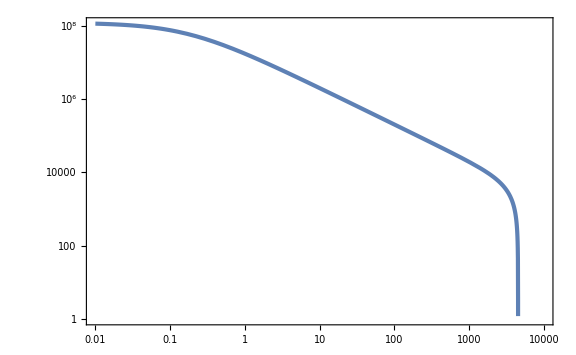

```mathematica
LogLogPlot[ξΓCOBE[ξg],{ξg,10^-2,10^4}]
```

```mathematica
ξgc=ξg/.Solve[ξΓCOBE[ξg]==0,ξg][[2]];ξgc//N
```

4502.24

```mathematica
Λ23COBE[ξg_]=Abs[Λ23/Mp]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ05COBE[ξg_]=Abs[Λ05/Mp]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ24COBE[ξg_]=Sqrt[Abs[Λ242/Mp^2]]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ06COBE[ξg_]=Sqrt[Abs[Λ062/Mp^2]]/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ25COBE[ξg_]=Abs[Λ253/Mp^3]^(1/3)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ07COBE[ξg_]=Abs[Λ073/Mp^3]^(1/3)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ26COBE[ξg_]=Abs[Λ264/Mp^4]^(1/4)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ08COBE[ξg_]=Abs[Λ084/Mp^4]^(1/4)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ27COBE[ξg_]=Abs[Λ275/Mp^5]^(1/5)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ09COBE[ξg_]=Abs[Λ095/Mp^5]^(1/5)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ28COBE[ξg_]=Abs[Λ286/Mp^6]^(1/6)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
Λ0tCOBE[ξg_]=Abs[Λ0t6/Mp^6]^(1/6)/.{λt->1/100,ξΓ->ξΓCOBE[ξg],δ->1,Mp->1};
```

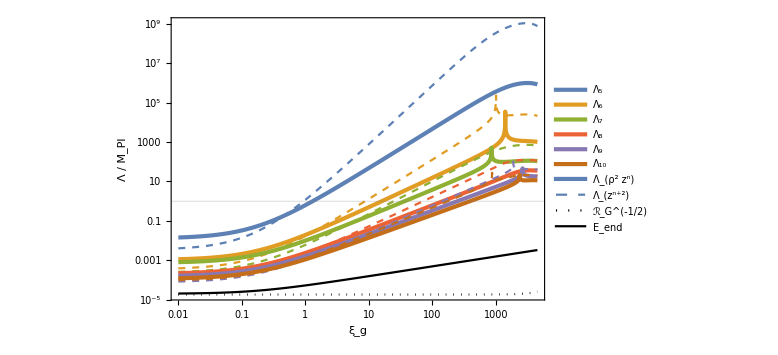

```mathematica
LogLogPlot[{Λ23COBE[ξg],Λ05COBE[ξg],Λ24COBE[ξg],Λ06COBE[ξg],Λ25COBE[ξg],Λ07COBE[ξg],Λ26COBE[ξg],Λ08COBE[ξg],Λ27COBE[ξg],Λ09COBE[ξg],Λ28COBE[ξg],Λ0tCOBE[ξg],0,0,Λorigin[ξg,ξΓCOBE[ξg]],(λ/4)^(1/4)1/Sqrt[ξg+ξΓCOBE[ξg]]/.{λ->1/100}},{ξg,10^-2,ξgc},GridLines->{None,{1}},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],Dashed},
{Color[2],AbsoluteThickness[3]},{Color[2],Dashed},
{Color[3],AbsoluteThickness[3]},{Color[3],Dashed},
{Color[4],AbsoluteThickness[3]},{Color[4],Dashed},
{Color[5],AbsoluteThickness[3]},{Color[5],Dashed},
{Color[6],AbsoluteThickness[3]},{Color[6],Dashed},
{Color[1],AbsoluteThickness[3]},{Color[1],Dashed},
{Black,Dotted},{Black}},FrameLabel->{Subscript[ξ, g],"Λ / M_Pl"},PlotLegends->Placed[LineLegend[{Subscript[Λ, 5],None,Subscript[Λ, 6],None,Subscript[Λ, 7],None,Subscript[Λ, 8],None,Subscript[Λ, 9],None,Subscript[Λ, 10],None,Subscript[Λ, ρ^2 z^("n")],Subscript[Λ, z^("n"+2)],"ℛ_G^(-1/2)","E_end"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->"Row",LegendMarkerSize->20],{0.37,0.82}]]
```

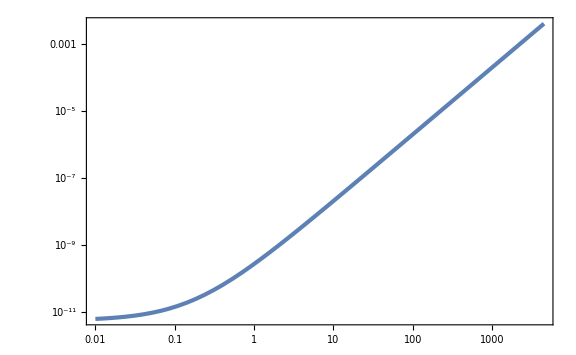

```mathematica
LogLogPlot[(1+6ξg)/(ξg+ξΓCOBE[ξg])2/55^2,{ξg,10^-2,ξgc}]
```